PROBLEM 1

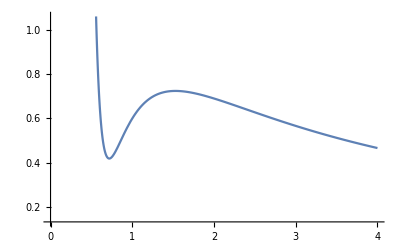

```mathematica
(* 1B *)
p[v_, t_]:=(8t)/(3v-1)-3/v^2
Plot[p[v, 0.9], {v, 0, 4}]
```

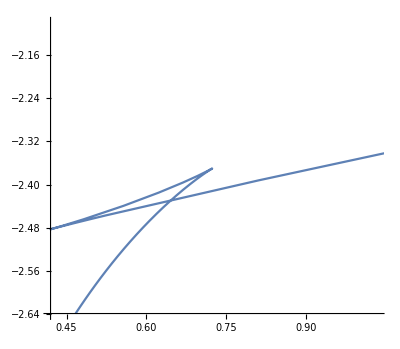

```mathematica
(* 1C *)
t := 0.9
v1:=-1
v2:=3
p[v_, t_]:=(8t)/(3v-1)-3/v^2
g[v_, t_]:=-t*Log[3v-1]+t/(3v-1)-9/(4v)
ParametricPlot[{p[v, 0.9], g[v, 0.9]}, {v,-1, 4}]
```

```mathematica
(* PROBLEM 2 *)
```

{{100,-160},{200,-35},{300,-4.2},{400,9},{500,16.9},{600,21.3}}

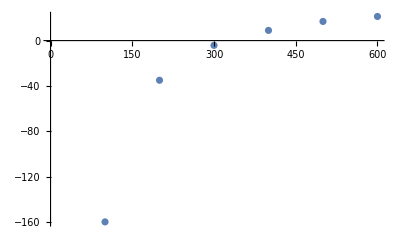

```mathematica
(* PROBLEM 3 *)
virdata={{100,-160},{200,-35},{300,-4.2},{400,9},{500,16.9},{600,21.3}}
(* 3a *)
(* T in Kelvin, B in cm^3/mol *)

ListPlot[virdata]
```

```mathematica
R := 8.314 (* J/(K mol) *)
FindFit[virdata, (2π)/3 σ^3 (1-u0/(R T)),{σ,u0},T]
```

FindFit::fdssnv: Search specification 3.12962 without variables should be a list with 1 to 4 elements.

FindFit[{{100,-160},{200,-35},{300,-4.2},{400,9},{500,16.9},{600,21.3}},64.1998 (1-341.535/T),{3.12962,2839.52},T]

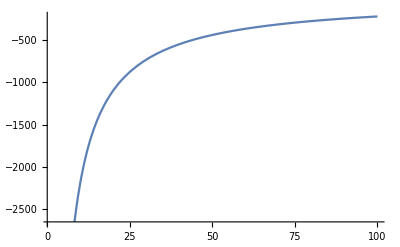

```mathematica
σ:=3.12962
u0:=2839.5182
B[T_]:=(2π)/3 σ^3 (1-u0)/(R T)
Plot[B[T], {T, 1, 100}]
```

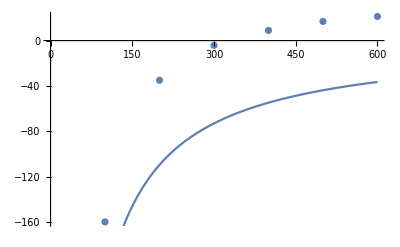

```mathematica
Show[ListPlot[virdata], Plot[B[T], {T, 0, 600}]]
```

```mathematica
(* 3c *)
N_a := 6.022 * 10^23

σ:=3.12962
u0:=2839.5182
σ*10^8*1/((6*10^23)^(1/3))

(* 3D *)
rho_nitrogen:=1.225 (* kg/m^3 *)
molar_mass:= 28 (* g/mol *)
R := 8.314 (* J/(K mol) *)
T = 293

P = 1.225/28 * 8.314 * 293

(* 3d *)

k = 1.38*10^-23
P = r*T*(ρ/m)^2*(2π)/3*σ*(1-u0/(k*T))

P = 8.314*293*(1.225/(28*0.001))^2*(2π)/3*(0.0312)^3*(1-(2839*1000)/(1.38*10^-23*293))
```

3.71057

293

106.575

1.38×10^-23

-(1.3487×10^27 r ρ^2)/m^2

-2.08245×10^29

```mathematica
(* 3d *)

T = (8*2829)/(27*8.314)
```

100.821